## numeric investigation

```mathematica
Quit[]
```

```mathematica
dispSimp = {devTerm_'[t]->OverDot[devTerm],devTerm_''[t]->OverDot[OverDot[devTerm]],aTerm_[t]->aTerm,  Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
```

equations of motion

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}});

(NonDimEOMmatrixForm=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, -1, 0}, {0, 0, α}})Subscript[DX, 1]).Subscript[𝒱, 1]+(({{1, 0, 0}, {0, -1, 0}, {0, 0, -α}})Subscript[DX, 2]).Subscript[𝒱, 2]-({{0}, {γ}, {0}})-𝒜-𝒟//Flatten)/.dispSimp//MatrixForm//TraditionalForm;
Subscript[DX, 1]=1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2));
Subscript[DX, 2]=1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2));
α=3/((Subscript[h, p]/Subscript[w, p])^2+1)(1/Subscript[w, p])^2;
Subscript[𝒱, 1]=({{Subscript[dx, 1]}, {Subscript[dy, 1]}, {term1}});
Subscript[𝒱, 2]=({{Subscript[dx, 2]}, {Subscript[dy, 2]}, {term2}});
γ=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]);
Subscript[ω, s]=Subscript[k, 1]/Subscript[m, p];
𝒜=({{ρ Subscript[C, D] Subscript[h, p] (-u+Subscript[x, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]}, {ρ Subscript[C, D] Subscript[w, p] (-v+Subscript[y, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]}, {0}})//Flatten;
𝒟=({{Subscript[c, x] (-Subscript[x, 1]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]+Subscript[c, x] (-Subscript[x, 2]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]}, {Subscript[c, y](-Subscript[y, 1]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1]+Subscript[c, y] (-Subscript[y, 2]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1]}, {1/1 1/Subscript[k, 1] Subscript[c, θ] Subscript[θ, p]'[t]}})//Flatten;
Subscript[L0, 1]=1;
(*greekTermsGeneralForTest={
Subscript[ω, s]^2->Subscript[k, 1]/Subscript[m, p],
α->(3 Subscript[L0, 1]^2)/(Subscript[w, p]^2+Subscript[h, p]^2),
γ->((g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))
}*)
(************************)
bigTermsToShort={(*(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 1][t]-Subscript[x, p][t])^2+(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])^2->l1,
(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 2][t]-Subscript[x, p][t])^2+(Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 2][t]+Subscript[y, p][t])^2->l2,*)
Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 1][t]-Subscript[x, p][t]->Subscript[dx, 1],
(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])->Subscript[dy, 1],
Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 2][t]-Subscript[x, p][t]->Subscript[dx, 2],
Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 2][t]+Subscript[y, p][t]->Subscript[dy, 2],
Subscript[w, p] (Sin[Subscript[θ, p][t]] Subscript[x, 1][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 1][t]+Subscript[y, p][t]))+Subscript[h, p] (-Cos[Subscript[θ, p][t]] Subscript[x, 1][t]+Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (-Subscript[y, 1][t]+Subscript[y, p][t]))->term1,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 2][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))+Subscript[w, p] (Sin[Subscript[θ, p][t]] Subscript[x, 2][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))->term2,
-(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])->-Subscript[dy, 1]
};
(dxdytermDetails=Table[Rule[bigTermsToShort[[i,2]] ,bigTermsToShort[[i,1]]],{i,1,Length[bigTermsToShort]}])//.dispSimp//MatrixForm//TraditionalForm
(************************)
NonDimEOMmatrixForm//TraditionalForm
```

(dx_1→w_p c(θ_p)+h_p s(θ_p)-x_p+x_1
dy_1→h_p c(θ_p)-w_p s(θ_p)+y_p-y_1
dx_2→-w_p c(θ_p)+h_p s(θ_p)-x_p+x_2
dy_2→h_p c(θ_p)+w_p s(θ_p)+y_p-y_2
term1→h_p (x_1 (-c(θ_p))+x_p c(θ_p)+(y_p-y_1) s(θ_p))+w_p ((y_p-y_1) c(θ_p)+x_1 s(θ_p)-x_p s(θ_p))
term2→h_p (x_2 c(θ_p)-x_p c(θ_p)+(y_2-y_p) s(θ_p))+w_p ((y_p-y_2) c(θ_p)+x_2 s(θ_p)-x_p s(θ_p))
-dy_1→h_p (-c(θ_p))+w_p s(θ_p)-y_p+y_1)

(x_p''(t)
y_p''(t)
θ_p''(t))==(-(ρ C_D h_p (x_p'(t)-u)^2)/m_p+dx_1 (1-1/(√(dx_1^2+dy_1^2)))+dx_2 (1-1/(√(dx_2^2+dy_2^2)))-(c_x (x_p'(t)-x_1'(t)))/k_1-(c_x (x_p'(t)-x_2'(t)))/k_1
-(ρ C_D w_p (y_p'(t)-v)^2)/m_p+dy_1 (1/(√(dx_1^2+dy_1^2))-1)+dy_2 (1/(√(dx_2^2+dy_2^2))-1)-(g m_p)/k_1-(c_y (y_p'(t)-y_1'(t)))/k_1-(c_y (y_p'(t)-y_2'(t)))/k_1
(3 term1 (1-1/(√(dx_1^2+dy_1^2))))/((h_p^2/w_p^2+1) w_p^2)-(c_θ θ_p'(t))/k_1-(3 term2 (1-1/(√(dx_2^2+dy_2^2))))/((h_p^2/w_p^2+1) w_p^2))

system parameters and inputs

```mathematica
systemVariables[ϵF_]:={
cFactor=0;  (* no Structural Damping *)
(*cFactor=0.1;  (* with Structural Damping *)*)
geometricAndMechanicParameters = {{g->9.81,Subscript[m, p]->1,Subscript[k, 1]->200(*,Subscript[L0, 1]->1*)},{Subscript[w, p]->2,Subscript[h, p]->1},{Subscript[c, x]->cFactor,Subscript[c, y]->cFactor,Subscript[c, θ]->cFactor}}//Flatten;
platForceVar={Subscript[v, y]->0,(*ϵF->1,*)Subscript[Ω, y]->2};
(*platformInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0} /.geometricAndMechanicParameters (*static case *)*)
platformInputs=  ({Subscript[x, 1][t]->0,Subscript[y, 1][t]->Subscript[v, y]+ϵF Sin[Subscript[Ω, y] t(*/Subscript[ω, s]*)],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}/.platForceVar//Flatten )/.geometricAndMechanicParameters   (* Ω[Hz] *);(*symmetric elevating case *)
environmentalParameters = {ρ->1.225, Subscript[C, D]->0} (* no drag forces *);
(*environmentalParameters = {ρ->1.225, Subscript[C, D]->1.1}*)
(* start conditions *) 
payloadEquibLocation = {Subscript[x, p][0]->Subscript[w, p],Subscript[y, p][0]->-(1/2 γ+Subscript[h, p]+1),Subscript[θ, p][0]->0}  /.geometricAndMechanicParameters(* the equilibrium point *);

allSystemBasicVariables = {geometricAndMechanicParameters,platformInputs,environmentalParameters,platForceVar}//Flatten;
}
```

### work functions

```mathematica
calcSol[Fmag_(*,T_*),startValues_ (*vec of 6*)]:={
systemVariables[Fmag];
(numericEOM = NonDimEOMmatrixForm//.dxdytermDetails  //.allSystemBasicVariables(*//. platformInputs//.environmentalParameters//. geometricAndMechanicParameters*));
numericEqs={X1'[t]==X2[t],
X2'[t]== (numericEOM[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (numericEOM[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (numericEOM[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];

(*Print["platformInputs : "];
Print[platformInputs];*)
initValuesEquations={X1[0]==startValues[[1]],X2[0]==startValues[[2]],X3[0]==startValues[[3]],					X4[0]==startValues[[4]],X5[0]==startValues[[5]],X6[0]==startValues[[6]]};
{"expectedPeriod by Forcing period:" ,
 expectedPeriod=2π/(Subscript[Ω, y](* /Subscript[ω, s]*))//. allSystemBasicVariables  //N,"[non-dim time]"};
(*{"expectedPeriod by Forcing period:" ,
 (*expectedPeriod=*)2π/(Subscript[Ω, y] /Subscript[ω, s])//. allSystemBasicVariables  //N,"[sec]"}*)
"T set to : ";
T=2*expectedPeriod;
sectionTime=9/10 T;

sol1 = NDSolve[ {numericEqs, initValuesEquations}, {X1, X2,X3,X4,X5,X6}, {t, 0, T},MaxSteps -> Floor[1000*T] ];
sol1[[1]]  (* the value/data to return *)

}
poincare[d_,ndrop_,nplot_,psize_]:=(
gg[prevStartValues_]:=({X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]}/.calcSol[d,(* T,*)prevStartValues])[[1]];
(*Print[calcSol[d, T,startValuesFromStatic]];*)
(*Print[gg[startValuesFromStatic[[All,2]]]];*)
extList=Drop[NestList[gg,startValuesFromEquib[[All,2]],nplot+ndrop],ndrop];
(*Print[extList];*)
pX=ListPlot[Transpose[{extList[[All,1]],extList[[All,2]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","x'"}];
pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
{pX,pY,pθ}
)
bifurcation[dmin_,dmax_,nd_,ndrop_,nplot_,psize_]:=(gg[{prevStartValues_,d_}]:=({{X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]},d}/.calcSol[d,(* T,*)prevStartValues])[[1]];
baseList[d_]:=Drop[NestList[gg,{startValuesFromEquib[[All,2]],d},nplot+ndrop],ndrop];
fX[{x_,d_}]:=(xElement = x[[1]]; {d,x[[1]]});
Print[{"number of solution to solve are :",nd(nplot+ndrop),"for T long each ", T}];
tableListX=Flatten[Table[fX/@(baseList[d]),{d,dmin,dmax,(dmax-dmin)/nd}],1];
(*tableListX=Flatten[Table[{(baseList[d])[[1,1]],{d,dmin,dmax,(dmax-dmin)/nd}],1];*)
(*Print[extList];*)
pX=ListPlot[tableListX,PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"ϵF","x"}];
(*pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
*)(*{pX,pY,pθ}*)
pX
)
```

### printing functions

```mathematica
plotParametricPlots[midT_]:={
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,midT},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,midT},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,midT},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,midT,T},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,midT,T},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,midT,T},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X2[t]}/.sol1,{t,0,T},AxesLabel->{"t","x'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X4[t]}/.sol1,{t,0,T},AxesLabel->{"t","y'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X6[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ'"},PlotRange->All(*,ColorFunction->"Rainbow"*)]}
}
```

### activate solution solver

```mathematica
systemVariables[0];allSystemBasicVariables
startdx=0.00;
startdy=0.00;
startdθ=0.01;
startdvx=0.00;
startdvy=0.00;
startdvθ=0.01;
startValuesFromEquib={  X1[0]==payloadEquibLocation[[1,2]]+startdx,X2[0]==0.0 + startdvx,
                                               X3[0]==payloadEquibLocation[[2,2]]+startdy,X4[0]==0.0 + startdvy,
                                                X5[0]==payloadEquibLocation[[3,2]]+startdθ,X6[0]==0.0 + startdvθ
}/.allSystemBasicVariables
```

{g→9.81,m_p→1,k_1→200,w_p→2,h_p→1,c_x→0,c_y→0,c_θ→0,x_1[t]→0,y_1[t]→0,x_2[t]→4,y_2[t]→y_1[t],ρ→1.225,C_D→0,v_y→0,Ω_y→2}

{X1[0]==2.,X2[0]==0.,X3[0]==-2.02453,X4[0]==0.,X5[0]==0.001,X6[0]==0.01}

```mathematica
calcSol[0.161,startValuesFromEquib[[All,2]]]
```

{{X1→InterpolatingFunction[{{0., 6.28319}}, <>],X2→InterpolatingFunction[{{0., 6.28319}}, <>],X3→InterpolatingFunction[{{0., 6.28319}}, <>],X4→InterpolatingFunction[{{0., 6.28319}}, <>],X5→InterpolatingFunction[{{0., 6.28319}}, <>],X6→InterpolatingFunction[{{0., 6.28319}}, <>]}}

```mathematica
sectionTime
```

5.65487

```mathematica
Manipulate[calcSol[f, startValuesFromEquib[[All,2]]];plotParametricPlots[sectionTime],{{f,0.01},0.0,0.085,Appearance-> "Open"}]
```

print plots

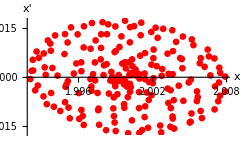
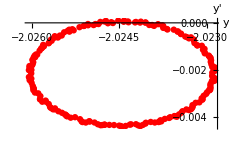
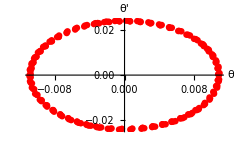

```mathematica
poincare[0.0011,100,200,0.02]
```

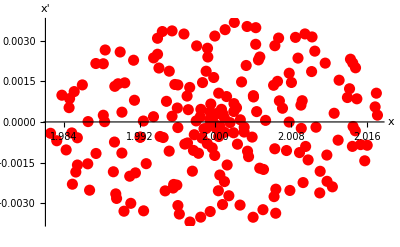
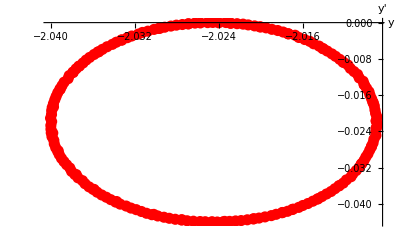
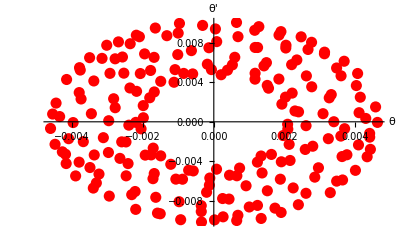

```mathematica
poincare[0.011,100,200,0.02]
```

```mathematica
poincare[0.161,100,200,0.02]
```

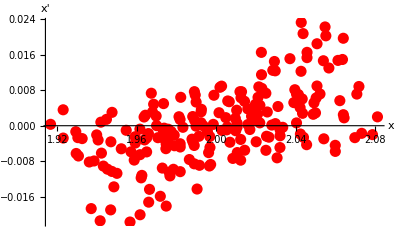
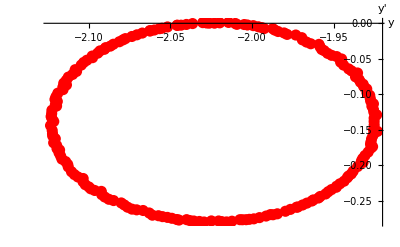
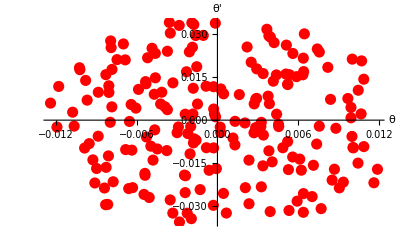

```mathematica
poincare[0.07,100,200,0.02]
```

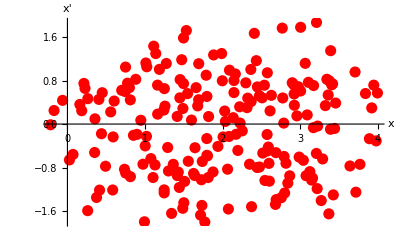
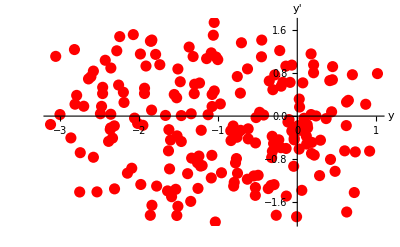
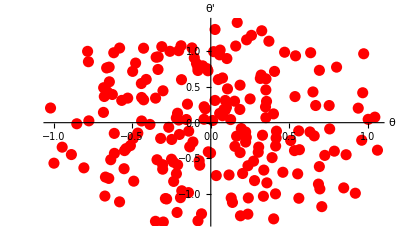

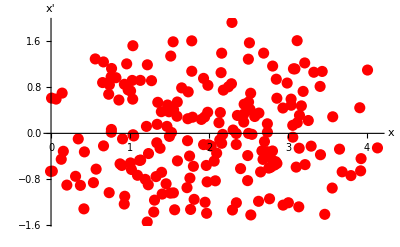
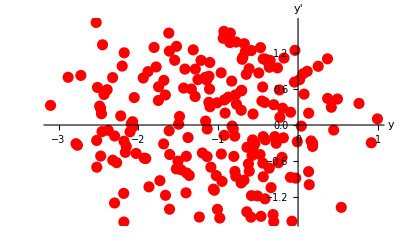
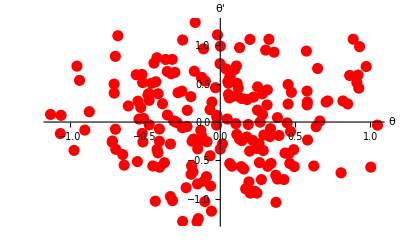

```mathematica
poincare[0.08,100,200,0.02]
```

{number of solution to solve are :,6000,for T long each ,6.28319}

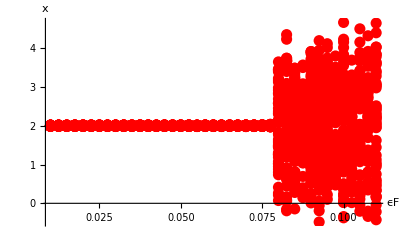

{number of solution to solve are :,7500,for T long each ,6.28319}

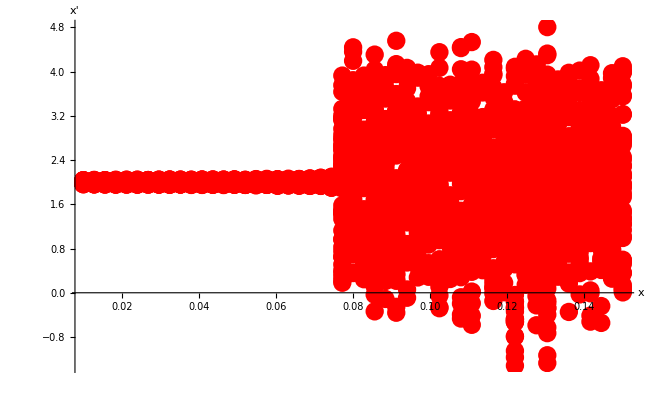

```mathematica
bifurcation[0.01,0.11,40,100,50,0.02]
```

{number of solution to solve are :,7500,for T long each ,6.28319}

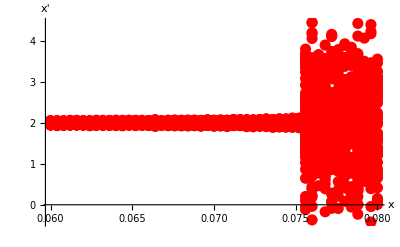

```mathematica
bifurcation[0.06,0.08,50,100,50,0.02]
```

{number of solution to solve are :,37500,for T long each ,6.28319}

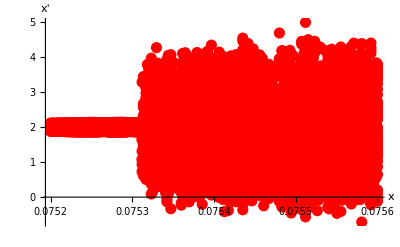

```mathematica
bifurcation[0.0752,0.0756,250,100,50,0.02]
```